# Lecture 7 - Momentum

### A Puzzle...

An Experiment on Energy
The shortest configuration of string joining three given points is the one where all three angles at the point of intersection equal 120°.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

How could you prove this fact experimentally by cutting three holes in a table and making use of three equal masses attached to the ends of strings (the other ends of which are connected), as shown below? (Assume that the strings are long, but they don’t need any particular length and all three lengths can be different.)

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Cut three holes in the table at the locations of the three given points. Drop the masses through the holes, and let the system reach its equilibrium position. The equilibrium position is the one with the lowest potential energy of the masses, that is, the one with the most string hanging below the table. In other words, it is the one with the least string lying on the table. This is the desired minimum-length configuration.

What are the angles at the vertex of the string? The tensions in all three strings are equal to m g. The vertex of the string is in equilibrium, so the net force on it must be zero. This implies that each string must bisect the angle formed by the other two. Therefore, the angles between the strings must all be 120°. □

### Momentum

#### Basics

For a single particle, we can rewrite F⃗=m a⃗ as

F⃗=(ⅆ p⃗)/ⅆt

where

p⃗=m v⃗

is the momentum of the particle. Momentum of a system is conserved if there are no external forces acting upon it; this makes momentum immensely useful when analyzing systems!

For a group of particles with masses m_j are positions (r⃗)_j, the total force on all of the particles equals

(F⃗)_tot=M (a⃗)_avg

where

M=∑_j m_j

(r⃗)_avg=(∑_j m_j(r⃗)_j)/M

(v⃗)_avg=(∑_j m_j(v⃗)_j)/M

(a⃗)_avg=(∑_j m_j(a⃗)_j)/M

we call (r⃗)_avg the center of mass. Defining the total momentum

(p⃗)_tot=M (v⃗)_avg

we can rewrite the force equation as

(F⃗)_tot=(ⅆ(p⃗)_tot)/ⅆt

In other words, we can treat all of the particles as one single particle of mass M and think about applying the force to this single mass at the center of mass (r⃗)_avg. While this is true for any infinitesimal time step, for it to be true for a length of time we cannot allow the particles to move relative to one another (in other words, the object cannot deform). We call such objects that don’t deform rigid objects, and we will deal with them nearly exclusively except in problems where we have inelastic collisions (coming shortly).

#### Conservation of Momentum

Example
A snowball is thrown against a wall. Where does its momentum go? Where does its energy go?

Solution
All of the snowball’s momentum goes into the earth, which then translates (and rotates) a tiny bit faster (or slower, depending on which way the snowball was thrown).

Denote the masses of the Earth and the snowball as M and m, respectively. In Earth’s rest frame, suppose the snowball was thrown with velocity v. Then conserving momentum the Earth’s final velocity would equal V≈(m v)/M. Hence, the Earth picks up kinetic energy

1/2 M ((m v)/M)^2=1/2 m v^2 (m/M)≪1/2 m v^2

There is also a rotational energy term of this same order of magnitude (that we will learn about next week). We see that essentially none of the snowball’s energy goes into the Earth. It therefore must all go into the form of heat, which melts some of the snow.

This is a general result for a small object hitting a large object: the large object picks up essentially all of the momentum but essentially none of the energy. □

### Elastic Collisions

#### General 1D Collisions

Example
Mass m moves with velocity v_1 to the right towards mass M moving with velocity v_2 to the left. After the collision, find the velocity v_3 of m and v_4 of M. 
Note: You do not need to worry about guessing the directions of v_3 and v_4 correctly - if you guess incorrectly either v_3 or v_4 will be negative. For example, if m/M→0 and M moves to the left after the collision, v_4 will be negative.

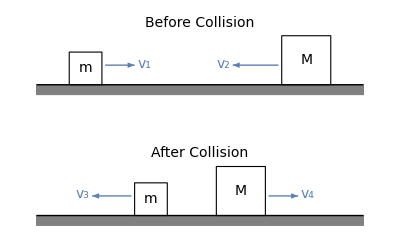

```mathematica
offset={0,-0.4};
centerPlot@Graphics[{Text[font["Before Collision",Italic],{0.5,0.19},{0,0}],{FaceForm[],EdgeForm[Black],Rectangle[{0.1,0.0},{0.2,0.1}],Rectangle[{0.75,0.0},{0.9,0.15}],Text[font["m",Italic],{0.15,0.05}],Text[font["M",Italic],{0.825,0.075}]},{Thick,Arrowheads[Medium],color1,Arrow[{{0.21,0.06},{0.3,0.06}}],Arrow[{{0.74,0.06},{0.6,0.06}}],Text[font@"v_1",{0.33,0.065}],Text[font@"v_2",{0.572,0.065}]},{EdgeForm[Gray],Gray,Rectangle[{0,-0.03},{1,0}]},{Line[{{0,0},{1,0}}]},Text[font["After Collision",Italic],offset+{0.5,0.19},{0,0}],{FaceForm[],EdgeForm[Black],Rectangle[offset+{0.3,0.0},offset+{0.4,0.1}],Rectangle[offset+{0.55,0.0},offset+{0.7,0.15}],Text[font["m",Italic],offset+{0.35,0.05}],Text[font["M",Italic],offset+{0.625,0.075}]},{Thick,Arrowheads[Medium],color1,Arrow[#+offset&/@{{0.29,0.06},{0.17,0.06}}],Arrow[#+offset&/@{{0.71,0.06},{0.8,0.06}}],Text[font@"v_3",offset+{0.14,0.065}],Text[font@"v_4",offset+{0.83,0.065}]},{EdgeForm[Gray],Gray,Rectangle[offset+{0,-0.03},offset+{1,0}]},{Line[#+offset&/@{{0,0},{1,0}}]}}]
```

Solution
Conservation of momentum and energy yield

m v_1-M v_2=-m v_3+M v_4

1/2 m v_1^2+1/2 M v_2^2=1/2 m v_3^2+1/2 M v_4^2

Solving this system of equations, we find

v_3=((M-m)v_1+2M v_2)/(M+m)

v_4=(2m v_1-(M-m)v_2)/(M+m)

In this lecture, we will explore two interesting limits of this result:

Case 1: M=m

When the two masses are identical, the final velocities becomes

v_3=v_2

v_4=v_1

In other words, the two masses trade velocities.

Case 2: m≪M

Define the small quantity ϵ≡m/M≪1. Instead of writing the solution in terms of M (the big mass) and m (the little mass), we will rewrite it in terms of M and ϵ. Recall that for -1<ϵ<1 we have the geometric series

1/(1+ϵ)=1-ϵ+ϵ^2-ϵ^3+···

Using this relation, Equation (TextNumbered) for v_3 become

v_3=((M-m)v_1+2M v_2)/(M+m)
=((1-m/M)v_1+2 v_2)/(1+m/M)
=((1-ϵ)v_1+2 v_2)/(1+ϵ)
={(1-ϵ)v_1+2 v_2}{1-ϵ+ϵ^2-ϵ^3+···}
={(1-ϵ)v_1+2 v_2}-{(1-ϵ)v_1+2 v_2}ϵ+(···)ϵ^2
=(v_1+2 v_2)-2(v_1+v_2)ϵ+(···)ϵ^2

where in the last step we grouped together all of the terms proportional to ϵ^0=1 and to ϵ^1, and we leave off in the (···) term all of the higher order terms in ϵ. Similarly, we can rewrite the solution to v_4 in Equation (TextNumbered) as

v_4=(2m v_1-(M-m)v_2)/(M+m)
=((2m)/M v_1-(1-m/M)v_2)/(1+m/M)
=(2ϵ v_1-(1-ϵ)v_2)/(1+ϵ)
={2ϵ v_1-(1-ϵ)v_2}{1-ϵ+ϵ^2-ϵ^3+···}
={2ϵ v_1-(1-ϵ)v_2}-{2ϵ v_1-(1-ϵ)v_2}ϵ+(···)ϵ^2
=(-v_2)+2(v_1+v_2)ϵ+(···)ϵ^2

To summarize, the values of v_3 and v_4 in terms of m/M=ϵ≪1 are

v_3=((1-m/M)v_1+2 v_2)/(1+m/M)≈v_1+2 v_2-2(v_1+v_2)m/M+(···)(m/M)^2

v_4=((2m)/M v_1-(1-m/M)v_2)/(1+m/M)≈-v_2+2(v_1+v_2)m/M+(···)(m/M)^2

First, note that to lowest order, we recover v_4≈-v_2, as expected. However, we cannot have v_4=-v_2 exactly and still conserve momentum, so the v_4 velocity will be slightly reduced by the small correction factor 2(v_1+v_2)m/M of order m/M. When we throw, for example, a ball at the ground, we can treat m/M≈0 for all practical purposes. Energy and momentum are still conserved because the Earth will pick up an extremely tiny change to its velocity.

To lowest order, the velocity of the small mass is given by v_3≈v_1+2 v_2. This makes total sense in the limit v_2=0, the familiar case where a ball strikes the ground and rebounds with the same velocity. When the wall itself is moving (v_2≠0), you can recover this result by moving into the rest frame of the wall. □

#### Useful Math Trick #1: Simplifying the Energy Relation

Consider the conservation of momentum and energy Equations (TextNumbered)-(TextNumbered) in the 1D collision problem above. Moving all of the m’s to one side and all the M’s to the other side

m (v_1+v_3)=M (v_2+v_4)

m (v_1^2-v_3^2)=M (v_4^2-v_2^2)

Rewriting this last equation,

m (v_1-v_3)(v_1+v_3)=M (v_4-v_2)(v_4+v_2)

Substituting in Equation (TextNumbered), we find the simple relation

v_1-v_3=v_4-v_2

This formula is exactly equivalent to the conservation of energy, we simply used the conservation of momentum formula to simply it. The advantage of using this alternative form of the conservation of energy is that it is linear in the velocities, which typically greatly simplifies the algebra involved.

In summary, for a 1D collision the conservation of energy and momentum can be written as

m (v_1+v_3)=M (v_2+v_4)

v_1-v_3=v_4-v_2

If you ever need to solve the general elastic collision problem for two masses, this is the way to do it. While you will certainly get the same answer as using the original conservation of energy formula, using the simplified version will be significantly cleaner.

#### Useful Math Trick #2: Taylor Series

In this section, we will discuss how Equations (TextNumbered)-(TextNumbered) are equivalent to taking the first order Taylor series approximations of v_3 and v_4 about the small parameter ϵ=m/M≈0.

First, consider the form of v_3[ϵ] given by

v_3[ϵ]=((1-ϵ)v_1+2 v_2)/(1+ϵ)

Rather than expanding the denominator into a geometric series as we did above, we write the Taylor series expansion of v_3[ϵ] as

v_3[ϵ]≈v_3[0]+(v_3'[0]ϵ)/(1!)+(v_3''[0]ϵ^2)/(2!)+···

Using Equation (TextNumbered), we compute

v_3[0]=v_1+2 v_2

v_3'[0]=-2(v_1+v_2)

Substituting into the Taylor series, we obtain

v_3[ϵ]≈(v_1+2 v_2)-2(v_1+v_2)ϵ+(···)ϵ^2
=(v_1+2 v_2)-2(v_1+v_2)ϵ+O[ϵ^2]

exactly as we found in Equation (TextNumbered). The notation O[ϵ^2] implies that all of the remaining terms are either proportional to ϵ^2, ϵ^3, or some higher power. Equation (TextNumbered) is called the first order Taylor approximation of v_3[ϵ] (since we are keeping all terms up to ϵ^1), and we can similarly compute the first order Taylor approximation of v_4[ϵ] as

v_4[ϵ]≈v_4[0]+(v_4'[0]ϵ)/(1!)+(v_4''[0]ϵ^2)/(2!)+···
=(-v_2)+2(v_1+v_2)ϵ+O[ϵ^2]

which is identical to Equation (TextNumbered) above. To summarize, the values of v_3 and v_4 in terms of m/M=ϵ≪1 are

v_3=((1-m/M)v_1+2 v_2)/(1+m/M)≈v_1+2 v_2-2(v_1+v_2)m/M+O[m/M]^2

v_4=((2m)/M v_1-(1-m/M)v_2)/(1+m/M)≈-v_2+2(v_1+v_2)m/M+O[m/M]^2

### Elastic Collisions

#### Newton’s Cradle

Newton’s cradle provides a fun testbed to build our intuition on collisions.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Example
Consider a Newton’s cradle consisting of two identical balls, one of which is pulled up and released from rest. What is the motion of the system?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
You likely know from playing with these toys that the balls will trade velocities. More precisely, the ball on the left will descend, trading its gravitational potential energy for kinetic energy. Right before it knocks into the second, stationary ball, we have the initial (i.e. pre-collision) state of the system. Denote the velocity of the left ball by v to the right, so that its energy equals 1/2 m v^2. The velocity and energy of the right ball are both zero. After the collision, the right ball will have velocity v to the right with energy 1/2 m v^2, while the left ball will be stationary. This solution trivially conserves energy and momentum (since the two balls just traded their values), and the system of equations has one unique solution so this must be the outcome of the collision. The right ball will proceed to move up until it has traded its kinetic energy for potential energy. Then the entire process will restart, but this time with all velocities pointed to the left. □

Example
Consider a Newton’s cradle consisting of multiple identical balls, one of which is pulled up and released from rest. What is the motion of the system?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
In all such problems, assume that there is a tiny bit of space between each ball. When the first (left-most) ball knocks into the second ball, it will transfer its full velocity and momentum. The second ball will then knock into the third ball, again transferring its entire velocity. This process continues until the velocity has moved through the fourth and finally the fifth ball, which will then rise into the air until it has traded its kinetic energy for gravitational potential energy. Then the process will restart with all velocities reversed. □

Example
Consider a Newton’s cradle consisting of multiple identical balls, two of which is pulled up and released from rest. What is the motion of the system?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
As above, we assume that there is a tiny bit of space between each ball. First the second ball (from the left) will knock into the third ball, transferring its entire velocity and starting the chain of transfers that will ultimately result in the last ball moving upwards. Soon after the second ball hits the third ball, the first ball will knock into the (now stationary) second ball, transferring all of its velocity and starting another series of transfers which will result in the fourth ball moving up nearly simultaneously with the fifth ball. So the two balls on the right end will move up until they trade their kinetic energy for gravitational potential energy, at which point the cycle will restart in the opposite direction. □

Of course, if you truly want to master Newton’s cradle, then you should try incorporating yourself into the cradle’s motion.

#### A Really Big Bounce

Example
A tennis ball with a small mass m_2 sits on top of a basketball with a large mass m_1. The bottom of the basketball is a height h above the ground, and the bottom of the tennis ball is a height h+d above the ground. The balls are dropped. To what height does the tennis ball bounce?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Note: Work in the approximation where m_1≫m_2, and assume that the balls bounce elastically. Also assume, for the sake of having a nice clean problem, that the balls are initially separated by a small distance, and that the balls bounce instantaneously.

Solution
Right before the basketball hits the ground, both balls move downward with speed (using 1/2 m v^2=m g h)

v=√(2g h)

Right after the basketball bounces off the ground, it moves upward with speed v, while the tennis ball still moves downward with speed v. The relative speed is therefore 2v. After the balls bounce off each other, the relative speed is still 2v (as can be seen by working in the heavy balls reference frame). Since the upward speed of the basketball essentially stays equal to v, the upward speed of the tennis ball is 2v+v = 3v. By conservation of energy, it will therefore rise to a height of H=d+(3v)^2/(2g). But v^2=2 g h, so that

H=d+9h

That is a huge increase in height! We can extend this setup to more balls (such as n=4 balls shown below where m_1≫m_2≫m_3≫m_4) and set the initial drop height to h=1meter.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

A stack of n=3 balls is shown in this YouTube video. With n=5 balls, the smallest one will bounce more than 1 kilometer and with n=12 balls the smallest ball will reach escape velocity for the Earth (although in that case the elasticity assumption is absurd, not to mention that you could not find 12 objects that satisfy m_1≫m_2≫···≫m_12). □

#### Advanced Section: A Geometric Series of Bounces

Example
A ball of mass m and initial speed v_0 bounces back and forth between a fixed wall and a block of mass M (with M≫m). M is initially at rest. Assume that the ball bounces elastically and instantaneously. The coefficient of kinetic friction between the block and the ground is μ. There is no friction between the ball and the ground and also no friction between the ball and the mass M (this means that we can completely ignore the rotation of the ball in our energy equation).

1. What is the speed of the ball after the n^th bounce of the block? 
2. How far does the block eventually move? 
3. How much total time does the block actually spend in motion? 
Work in the approximation where M≫m, and assume that μ is large enough so that the block comes to rest by the time the next bounce occurs.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
1. Let v_j be the speed of the ball after the j^th bounce, and let V_j be the speed of the block right after the j^th bounce. Then conservation of momentum and energy give

m v_j=M V_(j+1)-m v_(j+1)

1/2 m v_j^2=1/2 M V_(j+1)^2+1/2 m v_(j+1)^2

Solving this system of equations yields (in terms of ϵ≡m/M≪1)

V_(j+1)=(2 m)/(M+m)v_j≈2 ϵ v_j

v_(j+1)=(M-m)/(M+m)v_j≈(1-ϵ)/(1+ϵ)v_j≈(1-2ϵ) v_j

Therefore, after the n^th bounce,

v_n=(1-2ϵ)^n v_0

2. The total distance traveled by the block can be obtained by looking at the work done by the friction force F_f. Eventually, the ball has negligible energy, so all of its initial kinetic energy goes into heat from friction. Therefore, 1/2 m v_0^2=F_f d=(μ M g)d, which gives

d=(m v_0^2)/(2μ M g)

3. To find the total time, we can add up the times, t_n, the block moves after each bounce. Since force times time equals the change in momentum, we have F_f t_n=M V_n, and so (μ M g)t_n=M(2 ϵ v_(n-1))=2 M ϵ (1-2ϵ)^(n-1) v_0. Therefore,

t=∑_(n=1)^∞ t_n
=(2 ϵ v_0)/(μ g)∑_(n=0)^∞ (1-2ϵ)^n
=(2 ϵ v_0)/(μ g)1/(1-(1-2ϵ))
=v_0/(μ g)

This t is independent of the masses! Note that it is much larger than the result obtained in the case where the ball sticks to the block on the first hit, in which case the answer is (m v_0)/(μ M g). The total time is proportional to the total momentum that the block picks up, and the present answer is larger because the wall keeps transferring positive momentum to the ball, which then transfers it to the block. □

### Inelastic Collisions

Example
A mass M, initially moving at speed v, collides and sticks to a mass m, initially at rest. Assume M≫m. What are the final energies of the two masses, and how much energy is lost to heat, in:
1. The lab frame
2. The frame in which M is initially at rest?

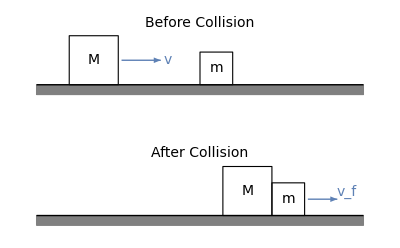

```mathematica
offset={0,-0.4};
centerPlot@Graphics[{Text[font["Before Collision",Italic],{0.5,0.19},{0,0}],{FaceForm[],EdgeForm[Black],Rectangle[{0.1,0.0},{0.25,0.15}],Rectangle[{0.5,0.0},{0.6,0.1}],Text[font["M",Italic],{0.175,0.075}],Text[font["m",Italic],{0.55,0.05}]},{Thick,Arrowheads[Medium],color1,Arrow[{{0.26,0.075},{0.38,0.075}}],Text[font["v",Italic],{0.4,0.075}]},{EdgeForm[Gray],Gray,Rectangle[{0,-0.03},{1,0}]},{Line[{{0,0},{1,0}}]},Text[font["After Collision",Italic],offset+{0.5,0.19},{0,0}],{FaceForm[],EdgeForm[Black],Rectangle[offset+{0.72,0.0},offset+{0.82,0.1}],Rectangle[offset+{0.57,0.0},offset+{0.72,0.15}],Text[font["m",Italic],offset+{0.77,0.05}],Text[font["M",Italic],offset+{0.645,0.075}]},{Thick,Arrowheads[Medium],color1,Arrow[#+offset&/@{{0.83,0.05},{0.92,0.05}}],Text[font@"v_f",offset+{0.95,0.072}]},{EdgeForm[Gray],Gray,Rectangle[offset+{0,-0.03},offset+{1,0}]},{Line[#+offset&/@{{0,0},{1,0}}]}}]
```

Solution
1. The initial energy equals E_i=1/2 M v^2. By conservation of momentum, the final speed of the combined masses is v_f=(M v)/(M+m)≈(1-m/M)v+O[m/M]^2. Therefore, the final energy of the small mass will be

E_(f,m)=1/2 m (1-m/M)^2 v^2
=1/2 m v^2-m v^2(m/M)+1/2 m (v^2(m/M))^2
≈1/2 m v^2+O[m/M]^2

As we found in the 1D collision problem, the last approximation is equivalent to taking the first order Taylor series of E_(f,m) about the small quantity m/M≪1, as you can see by rewriting E_(f,m) in terms of M and ϵ M=m and then taking the first order Taylor approximation about ϵ. Similarly, the final energy of the large mass equals

E_(f,M)=1/2 M (1-m/M)^2 v^2
≈1/2 M v^2-m v^2+O[m/M]^2

where again we have taken the first order Taylor approximation about ϵ=m/M. Using these two results, the change in energy is given by

E_i-(E_m+E_M)=1/2 m v^2

which is the energy lost as heat.

2. In this frame, mass m has initial speed v, so its initial energy is E_i=1/2 m v^2. By conservation of momentum, the final speed of the combined masses is v_f=(m v)/(M+m)≈m/M v+O[m/M]^2 and hence the final energies are

E_m=1/2 m (m/M)^2 v^2≈(m/M)^2 E_i≈0

E_M=1/2 M (m/M)^2 v^2≈m/M E_i≈0

This negligible final energy means that the change in energy equals

E_i-(E_m+E_M)=1/2 m v^2

which is the energy lost as heat, in agreement with the result found in the lab frame. □

Technical note: You might wonder why we took the first order Taylor approximation of E_(f,m) and E_(f,M) rather than taking, say, the zeroth order or second order Taylor approximation. The zeroth order Taylor approximation would yield E_(f,m)=0+O[m/M] and E_(f,M)=1/2 M v^2+O[m/M], which is not very informative. It only tells us that to zeroth order, energy is conserved in inelastic collisions, and any deviations from this conservation of energy are at least of order m/M. But unlike elastic collisions (where energy is exactly conserved), we wanted to find out what the change in energy was in this inelastic collision, so we go one additional order higher in the Taylor approximation until we get a non-trivial result. You may also repeat the problem to third order and find the complete, exact solution

E_i-(E_m+E_M)=1/2 m v^2+(1/2 m v^2)m/M-(1/2 m v^2)(m/M)^2

but note that the second term (1/2 m v^2)m/M is a tiny fraction m/M as large as the first term 1/2 m v^2, and the third term is negligible compared to both terms. In physics, we typically want the lowest order non-zero result to a problem, so when m/M≪1 we are happy to approximate this result as

E_i-(E_m+E_M)≈1/2 m v^2

### Between Elastic and Inelastic

In this section, we will explore the amazing, interactive PhET collision simulation. Through this simulator, you can not only recap all of the results seen above, but also push beyond them.

Have you ever wondered why we use the words perfectly elastic and perfectly inelastic? What lies in between these two limits?

Open up the collision simulator (this might require Internet Explorer) and get some bearings on what you can control. Hit Play and you can collide the two masses; hit Restart and you can do it all over again. But everything is interactive! The two objects can be dragged to different initial positions. Their masses (and their velocities in the More Data tab at the bottom) can be controlled, and different aspects of the collision can be viewed using the checkboxes on the right.

Here are some questions that I encourage you to explore:

What happens to the center of mass before and after a collision?

What happens if the two objects have the exact same mass (as we found for Newton’s cradle)? What if one is slightly heavier?

What happens if one ball is much heavier than the other? Can you recoup the results of the Bouncing Balls problem?

Is momentum conserved? Is energy conserved?

How do these answers change in a perfectly inelastic collision? Can you recover the results of the inelastic collision problem?

Note that on the right, there is a slider which lets you alter the elasticity anywhere between 100% (the perfectly elastic limit) and 0% (the perfectly inelastic limit). To understand an intermediate value, we need to define elasticity.

For a 1D collision, elasticity is defined as the relative speed between two objects after a collision divided by what this relative speed would have been in a perfectly elastic collision,

(relative speed between two centers after collision) = (elasticity)×(relative speed of two centers in a perfectly elastic collision)

For example, if elasticity=0 %, there will be no relative speed between the two objects after a collision and they will stick together. If elasticity=100 %, the collision will be perfectly elastic. If elasticity is 30%, then the relative speeds between the two objects will be 3/10 of what it would be in an elastic collision; this constraint together with the conservation of momentum fixes the final velocities of an object.

There is also an Advanced tab at the top of the simulator which takes you a 2D pool table. Use this simulator to explore the following problems.

For which collisions is momentum conserved? For which collisions is energy conserved?

What happens to the center of mass as the simulation progresses?

Use the More Data tab to set one of the balls to be stationary and have the other ball knock into it. Turn the Show Paths feature on. What do you notice about the angle between the two objects after the collision?

Tune the elasticity to somewhere between 0 % and 100 %. Can you understand the resulting collision? How do the questions above change?

Finally, we mention that in 2D, the definition of elasticity is the same, except that it only applies to the component of the relative velocity along the "line of action," which is the line connecting the centers of the balls at the moment of collision. The relative speed of the two objects perpendicular to the line of action is not affected.

## Mathematica Initialization

```mathematica
(* Font size for all plots in this notebook *)
ft=16;
```

```mathematica
(* Primary colors for figures *)
colors={color1,color2,color3,color4,color5,color6}={ColorData[97][1],ColorData[97][10],ColorData[97][5],ColorData[97][6],ColorData[97][9],Lighter@ColorData[97][7]};
(* Secondar colors for backgrounds *)
backgroundColors={backgroundColor1}={RGBColor[0.99, 0.97432, 0.91748]};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
$Assumptions=By>0&&Bz>0&&c>0&&0<ϕ<2π&&0≤ψ≤2π;
```

```mathematica
(* To make x̂-, ŷ-, and ẑ-direction vectors in a Graphics *)
Clear[directionVectors]
directionVectors[base_,size_:1]:={Black,Arrowheads[Small],Arrow[{{base,base+size{0.1,0}},{base,base+size{0,0.1}},{base,base+size{-0.05,-0.05}}}],Text[font@"x̂",base+size{0.12,0}],Text[font@"ŷ",base+size{0,0.12}],Text[font@"ẑ",base+size{-0.06,-0.065}]}
```